## Distribution plots of hedge performance

### Customised plots

A customised Box-Whisker plot

```mathematica
ModifiedBoxWhiskerChart[d_]:=Module[{s},
s=Quantile[#,{0.01,0.25, 0.5, 0.75, 0.99}]&/@d;
BoxWhiskerChart[s, Method->{"BoxRange"->Identity}]
]
```

```mathematica
ModifiedBoxWhiskerChart[d_,leg_,title_]:=Module[{s},
s=Quantile[#,{0.05,0.25, 0.5, 0.75, 0.95}]&/@d;
BoxWhiskerChart[s, Method->{"BoxRange"->Identity},ChartLabels->{leg}, PlotTheme->"Classic", ChartStyle->Darker[Green], PlotLabel->title]
]
```

Function for creating various plots (note that bw-plots are capped at 1%/99%-quantile levels)
This function is rough - used only to select the appropriate plot type

```mathematica
AllPlots[pos_]:=Module[{d, p1, p2, p3, p4,p5},
d=data[[pos]];
p1=ModifiedBoxWhiskerChart[d];
p2=SmoothHistogram[d, Automatic, "PDF",PlotRange->Full,PlotLegends->{ToString[#]&/@legend[[pos]]}];
sk1=SmoothKernelDistribution[d[[1]]];
sk2=SmoothKernelDistribution[d[[2]]];
p3=LogPlot[{PDF[sk1,x], PDF[sk2,x]}, {x,-2000,2000},PlotRange->Full];
m1=Ceiling[Max[Abs[{Min[Quantile[#,0.01]&/@d], Max[Quantile[#, 0.99]&/@d]}]],0.1];
p4=DistributionChart[d,PlotTheme->"Classic",PlotRange->{-m1,m1}];
p5=PairedHistogram[d[[1]], d[[2]], Automatic, "PDF"];
Grid[{{p1,p2,SpanFromLeft},{p3,p4,p5}}]
]
```

```mathematica
DistPlot[pos_]:=Module[{d},
d=data[[pos]];
m1=Ceiling[Max[Abs[{Min[Quantile[#,0.05]&/@d], Max[Quantile[#, 0.95]&/@d]}]],0.1];
p4=DistributionChart[d,PlotTheme->"Classic",PlotRange->{-m1,m1},ChartLegends->{ToString[#]&/@legend[[pos]]}];
p4
]
```

### Load data

```mathematica
dataDirectory = "/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/";
prices =Import[dataDirectory <> "__prices.csv"];
```

```mathematica
fn=FileNames["PNL__KDE*BULLISH__4088__90*.csv", dataDirectory];
price=Select[prices, StringContainsQ[#[[2]], "BULLISH__4088__90"]&][[1]][[-1]];
fname="KDE_BULLISH_4088_90";
```

```mathematica
fn=FileNames["PNL__KDE*CALM__8367__90*.csv", dataDirectory];
price=Select[prices, StringContainsQ[#[[2]], "CALM__8367__90"]&][[1]][[-1]];
fname="KDE_CALM_8367_90";
```

```mathematica
fn=FileNames["PNL__KDE*COVID__9804__90*.csv", dataDirectory];
price=Select[prices, StringContainsQ[#[[2]], "COVID__9804__90"]&][[1]][[-1]];
fname="KDE_COVID_9804_90";
```

```mathematica
fn=FileNames["PNL__SVCJ*BULLISH__4088__90*.csv", dataDirectory];
price=Select[prices, StringContainsQ[#[[2]], "BULLISH__4088__90"]&][[1]][[-1]];
fname="SVCJ_BULLISH_4088_90";
```

```mathematica
fn=FileNames["PNL__SVCJ*CALM__8367__90*.csv", dataDirectory];
price=Select[prices, StringContainsQ[#[[2]], "CALM__8367__90"]&][[1]][[-1]];
fname="SVCJ_CALM_8367_90";
```

```mathematica
fn=FileNames["PNL__SVCJ*COVID__9804__90*.csv", dataDirectory];
price=Select[prices, StringContainsQ[#[[2]], "COVID__9804__90"]&][[1]][[-1]];
fname="SVCJ_COVID_9804_90";
```

```mathematica
data = Import[#]&/@fn;
data=DeleteCases[Flatten[data[[#]]],_?StringQ]&/@Range[Length[data]];
data = data /price;
```

```mathematica
Dimensions[data]
```

{23}

```mathematica
fn
```

{/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__BLACK_SCHOLES__DeltaGammaHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__BLACK_SCHOLES__DeltaHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__BLACK_SCHOLES__DeltaVegaHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__CGMY__DeltaGammaHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__CGMY__DeltaHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__HESTON__DeltaGammaHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__HESTON__DeltaHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__HESTON__DeltaVegaHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__HESTON__MinimumVarianceHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__MERTON__DeltaGammaHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__MERTON__DeltaHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__MERTON__DeltaVegaHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__MERTON__MinimumVarianceHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__SVCJ__DeltaGammaHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__SVCJ__DeltaHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__SVCJ__DeltaVegaHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__SVCJ__MinimumVarianceHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__SVJ__DeltaGammaHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__SVJ__DeltaHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__SVJ__DeltaVegaHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__SVJ__MinimumVarianceHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__VARIANCE_GAMMA__DeltaGammaHedge__CALM__8367__90__100000.csv,/Users/nat/Documents/GitHub/hedging_cc/_output/hedges/pnl/20210721_162954/PNL__SVCJ__VARIANCE_GAMMA__DeltaHedge__CALM__8367__90__100000.csv}

```mathematica
legend=StringSplit[StringSplit[#,"/"][[-1]], "__"][[2;;-3]]&/@fn;
```

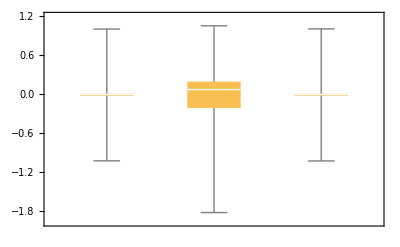
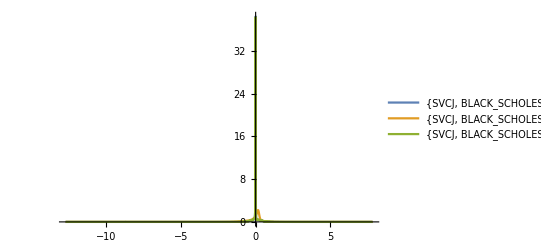
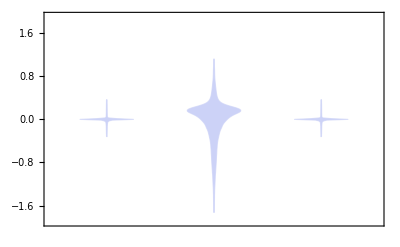
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
pos=Flatten[Position[StringMatchQ[#, "*BLACK*"]&/@ fn, True]];
AllPlots[pos]
```

```mathematica
legend[[pos]]
```

(SVCJ | BLACK_SCHOLES | DeltaGammaHedge | CALM | 8367
SVCJ | BLACK_SCHOLES | DeltaHedge | CALM | 8367
SVCJ | BLACK_SCHOLES | DeltaVegaHedge | CALM | 8367)

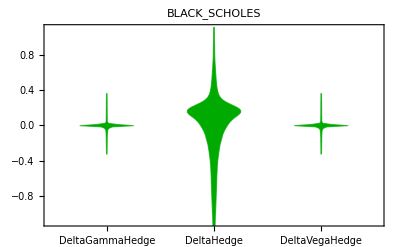

```mathematica
pos=Flatten[Position[StringMatchQ[#, "*BLACK*"]&/@ fn, True]];
dp=DistPlot[pos,ToString[#]&/@legend[[pos,3]], legend[[1,2]]]
```

{4,5}

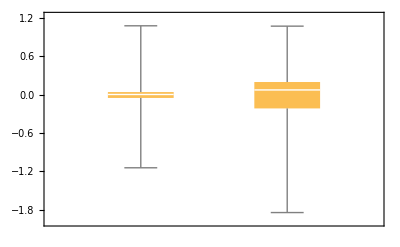
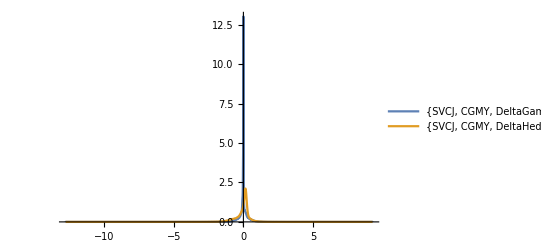
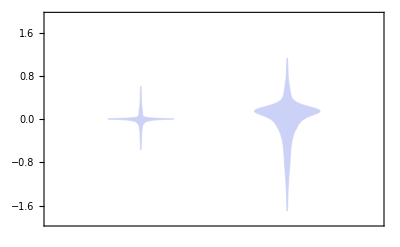
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
pos=Flatten[Position[StringMatchQ[#, "*CGMY*"]&/@ fn, True]]
AllPlots[pos]
```

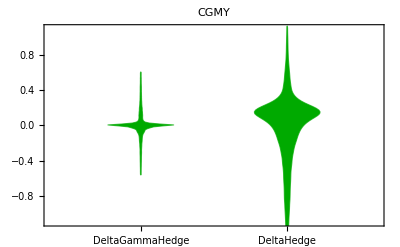

```mathematica
pos=Flatten[Position[StringMatchQ[#, "*CGMY*"]&/@ fn, True]];
dp=DistPlot[pos,ToString[#]&/@legend[[pos,3]], legend[[4,2]]]
```

{6,7,8,9}

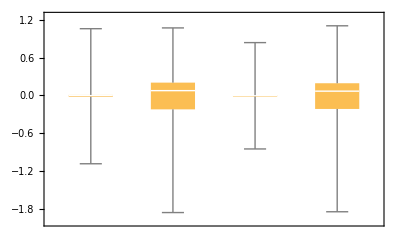
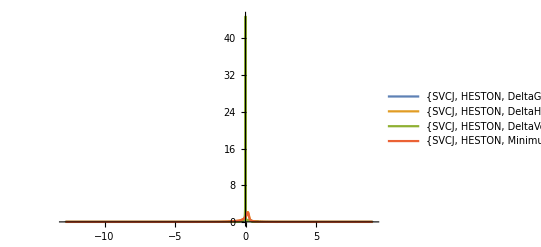
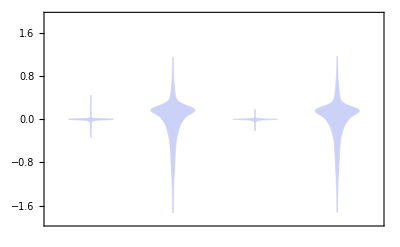
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
pos=Flatten[Position[StringMatchQ[#, "*HESTON*"]&/@ fn, True]]
AllPlots[pos]
```

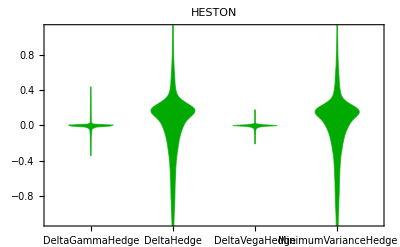

```mathematica
pos=Flatten[Position[StringMatchQ[#, "*HESTON*"]&/@ fn, True]];
dp=DistPlot[pos,ToString[#]&/@legend[[pos,3]], legend[[pos[[1]],2]]]
```

{14,15,16,17}

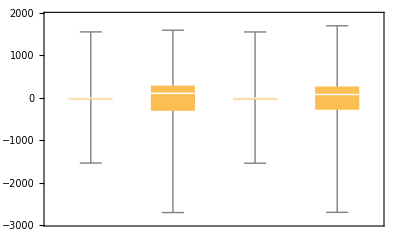
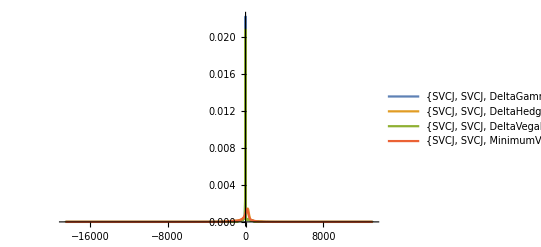
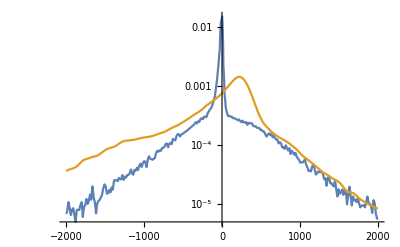
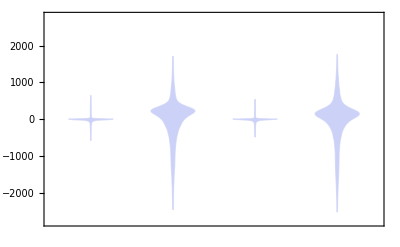
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
pos=Flatten[Position[StringMatchQ[#, "*__*__*SVCJ*"]&/@ fn, True]]
AllPlots[pos]
```

{18,19,20,21}

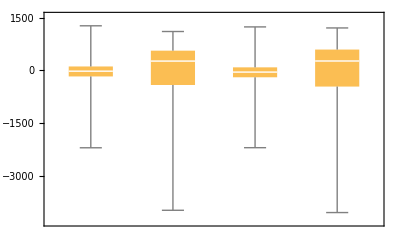
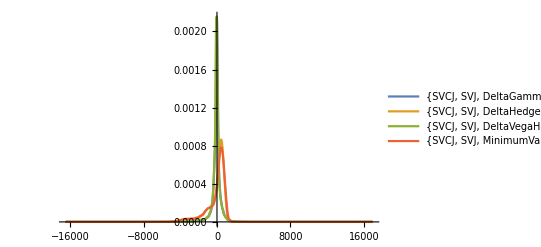
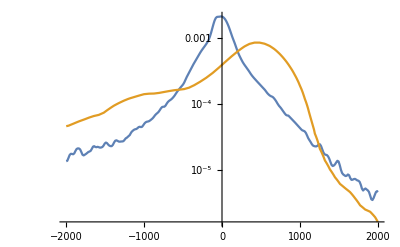
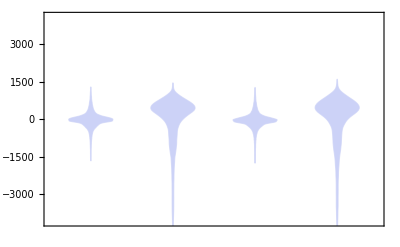
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
pos=Flatten[Position[StringMatchQ[#, "*SVJ*"]&/@ fn, True]]
AllPlots[pos]
```

{2,5,7,11,15,19,23}

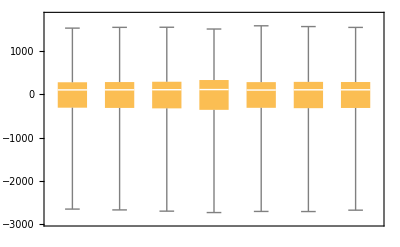
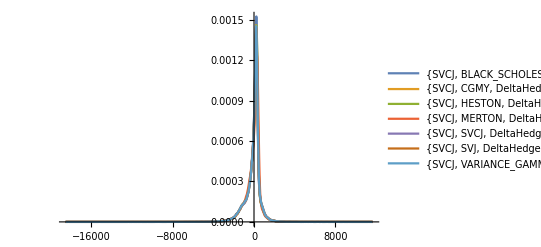
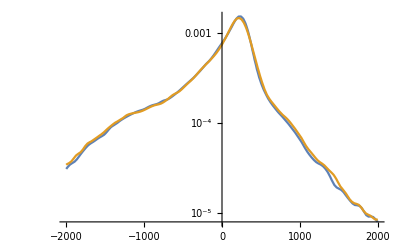
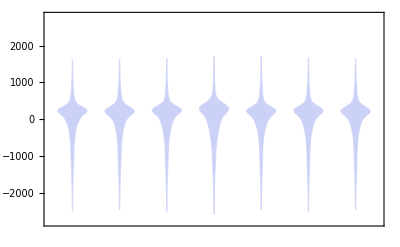
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
pos=Flatten[Position[StringMatchQ[#, "*DeltaHedge*"]&/@ fn, True]]
AllPlots[pos]
```

{1,4,6,10,14,18,22}

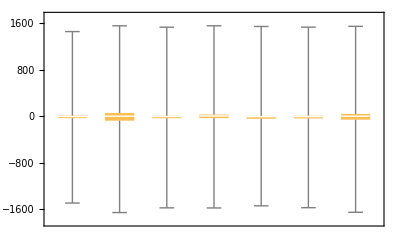
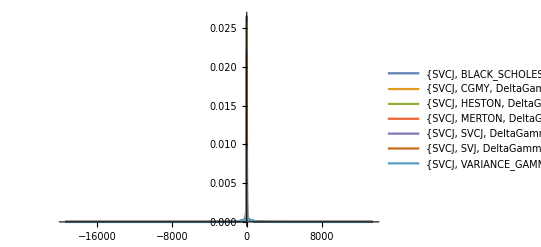
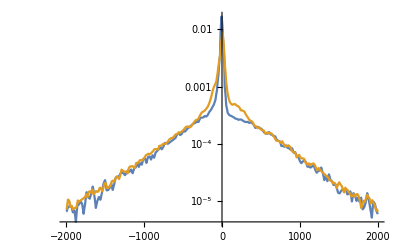
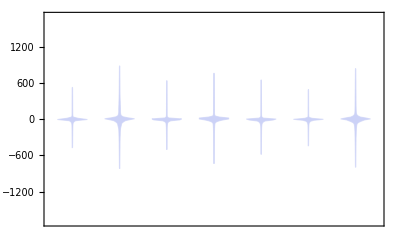
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
pos=Flatten[Position[StringMatchQ[#, "*DeltaGammaHedge*"]&/@ fn, True]]
AllPlots[pos]
```

{3,8,12,16,20}

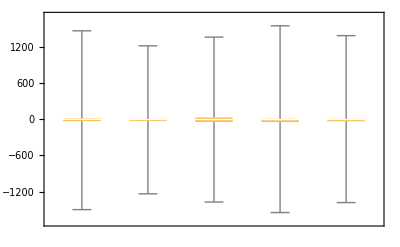
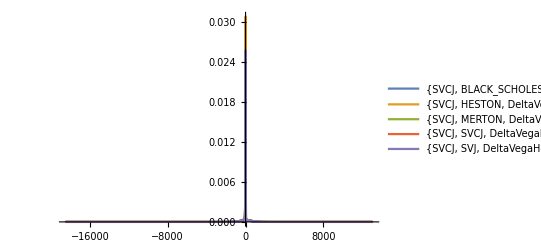
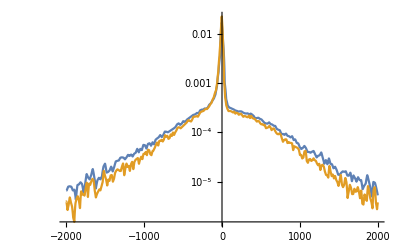
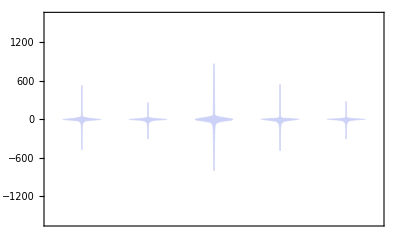
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
pos=Flatten[Position[StringMatchQ[#, "*DeltaVegaHedge*"]&/@ fn, True]]
AllPlots[pos]
```

{9,13,17,21}

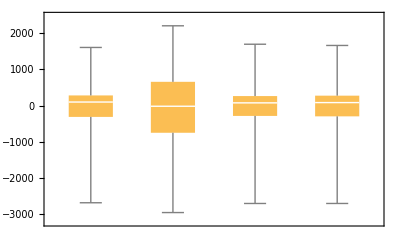
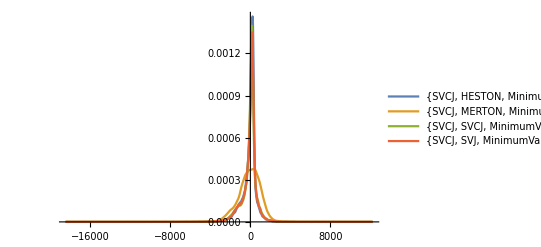
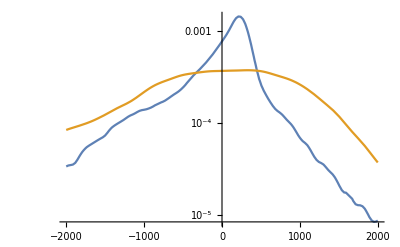
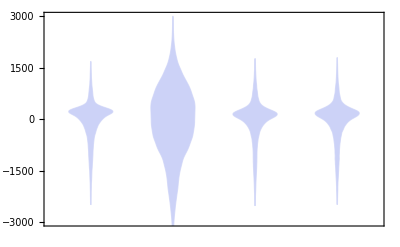
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
pos=Flatten[Position[StringMatchQ[#, "*MinimumVariance*"]&/@ fn, True]]
AllPlots[pos]
```

{2,1,4,6,10,14,18,22}

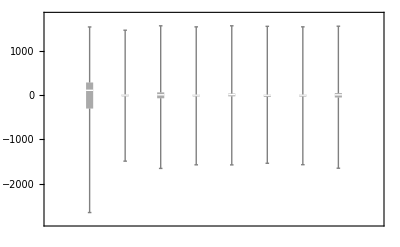
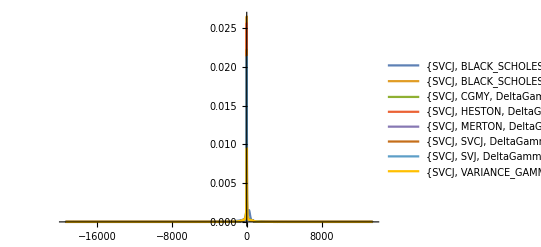
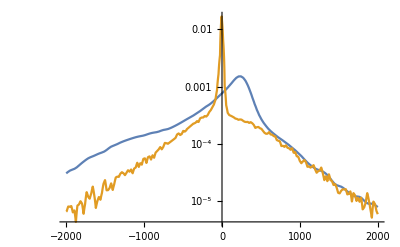
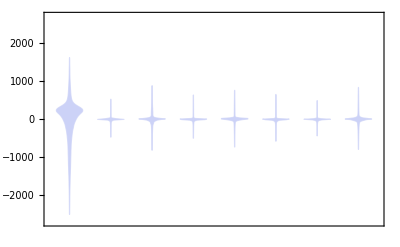
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
pos=Flatten[Position[StringMatchQ[#, "*DeltaGamma*"]&/@ fn, True]];
PrependTo[pos, 2]
AllPlots[pos]
```

```mathematica
pos1=Flatten[Position[StringMatchQ[#,"*__*__*SVCJ*"]&/@ fn, True]]
```

{14,15,16,17}

{2,1,8,12,20,14,22,4}

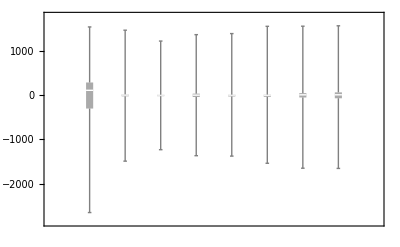
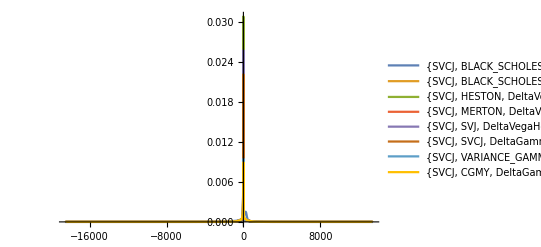
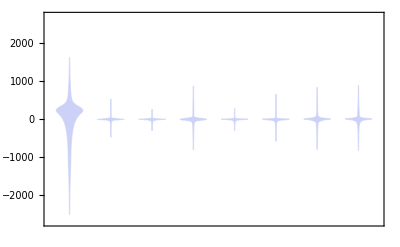
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
pos={};
d=DeleteCases[Flatten[data[[#]]],_?StringQ]&/@Range[Dimensions[data][[1]]];
models={"*BLACK*", "*HESTON*", "*MERTON*", "*SVJ*", "*__*__*SVCJ*", "*VARIANCE_GAMMA*", "*CGMY*"};
pos2=PositionIndex[Quantile[#, 0.05]&/@d];
For[k=1, k<= Length[models], k++,
pos1=Flatten[Position[StringMatchQ[#, models[[k]]]&/@ fn, True]];
AppendTo[pos,pos2[Max[Keys[pos2[[pos1]]]]][[1]]];
]
PrependTo[pos, 2]
plot=AllPlots[pos]
Export[NotebookDirectory[] <> fname <> ".pdf", plot]
```

Model mit niedrigster Varianz / Stabw.
Model mit niedrigstem 5% ES

{2,1,8,10,20,14,22,4}

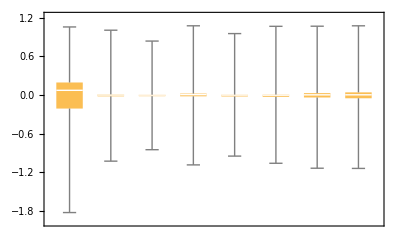
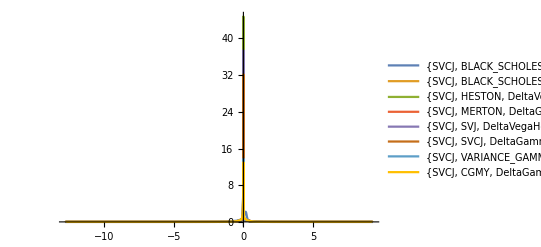
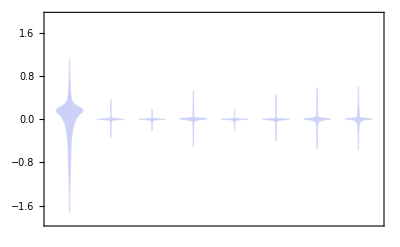
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

/Users/nat/Documents/GitHub/hedging_cc/_mathematica/SVCJ_CALM_8367_90.pdf

```mathematica
pos={};
d=DeleteCases[Flatten[data[[#]]],_?StringQ]&/@Range[Dimensions[data][[1]]];
models={"*BLACK*", "*HESTON*", "*MERTON*", "*SVJ*", "*__*__*SVCJ*", "*VARIANCE_GAMMA*", "*CGMY*"};
pos2=PositionIndex[Quantile[#, 0.1]&/@d];
For[k=1, k<= Length[models], k++,
pos1=Flatten[Position[StringMatchQ[#, models[[k]]]&/@ fn, True]];
AppendTo[pos,pos2[Max[Keys[pos2[[pos1]]]]][[1]]];
]
PrependTo[pos, 2]
plot=AllPlots[pos]
Export[NotebookDirectory[] <> fname <> ".pdf", plot]
```

{2,1,8,12,20,16,22,4}

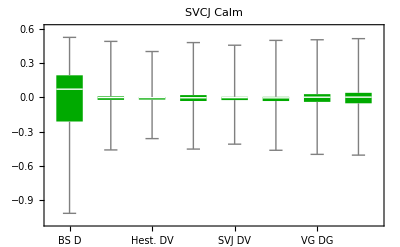

/Users/nat/Documents/GitHub/hedging_cc/_mathematica/SVCJ_CALM_8367_90.pdf

```mathematica
pos={};
d=DeleteCases[Flatten[data[[#]]],_?StringQ]&/@Range[Dimensions[data][[1]]];
models={"*BLACK*", "*HESTON*", "*MERTON*", "*SVJ*", "*__*__*SVCJ*", "*VARIANCE_GAMMA*", "*CGMY*"};
(* pos2=PositionIndex[Quantile[#, 0.1]&/@d]; *)
q=Quantile[#,0.05]&/@d;
es=Table[Mean[Select[d[[k]],#<=q[[k]]&]], {k,1,Length[d]}];
pos2 = PositionIndex[es];
For[k=1, k<= Length[models], k++,
pos1=Flatten[Position[StringMatchQ[#, models[[k]]]&/@ fn, True]];
AppendTo[pos,pos2[Max[Keys[pos2[[pos1]]]]][[1]]];
]
leg= {"BS D", "BS DG", "Hest. DV", "Mert. DV", "SVJ DV","SVCJ DV", "VG DG", "CGMY DG"};
PrependTo[pos, 2]
(*plot=DistPlot[pos, leg, "SVCJ Calm"]*)
plot=ModifiedBoxWhiskerChart[d[[pos]],leg, "SVCJ Calm"]
Export[NotebookDirectory[] <> fname <> ".pdf", plot]
```

-Graphics-

```mathematica
t=Table[
{q1=Quantile[d[[k]],0.05], q2=Quantile[d[[k]], 0.95]};{Min[d[[k]]],Mean[Select[d[[k]],#<=q1&]],
Mean[Select[d[[k]],#>=q2&]], Max[d[[k]]], 100 StandardDeviation[d[[k]]]/price}, {k,pos}]//Round[#,0.01]&;
```

```mathematica
max=Max/@Abs[Transpose[t]];
min=Min/@Abs[Transpose[t]];
maxpos=Flatten[Table[Append[#,i]&/@Position[Abs[t[[All,i]]],max[[i]]],{i,1,Length@max}],1];
minpos=Flatten[Table[Append[#,i]&/@Position[Abs[t[[All,i]]],min[[i]]],{i,1,Length@min}],1];
t2=MapAt[Style[#,Darker[Green]]&,MapAt[Style[#,Red]&,t,maxpos],minpos];
```

```mathematica
Grid[Prepend[Prepend[t2, {"Min", "5% ES", "95% ES", "Max", "Hedge error"}]ᵀ, Join[{""},leg]], Alignment->Right]
```

| BS D | BS DG | Hest. DV | Mert. DV | SVJ DV | SVCJ DV | VG DG | CGMY DG
Min | -12.63 | -8.68 | -12.75 | -6.32 | -7.79 | -12.75 | -12.73 | -12.74
5% ES | -1.56 | -0.85 | -0.71 | -0.79 | -0.78 | -0.89 | -0.96 | -0.97
95% ES | 0.88 | 0.82 | 0.69 | 0.77 | 0.79 | 0.88 | 0.89 | 0.9
Max | 7.74 | 5.19 | 7.79 | 4.15 | 7.78 | 8.99 | 8.97 | 9.25
Hedge error | 0.04 | 0.02 | 0.02 | 0.02 | 0.02 | 0.02 | 0.03 | 0.03

```mathematica
Export[NotebookDirectory[] <> fname <> "_graph.pdf", %]
```

/Users/nat/Documents/GitHub/hedging_cc/_mathematica/SVCJ_CALM_8367_90_graph.pdf